```mathematica
maxdeg = 3;
```

```mathematica
deg = Flatten[Table[Subscript[f, i,j]->If[i+j>maxdeg,0,Subscript[f, i,j]],{i,0,3},{j,0,3}]];
```

```mathematica
deg1 = Flatten[Table[Subscript[f, i,j]->If[i+j==1,Subscript[f, i,j],0],{i,0,3},{j,0,3}]];
```

```mathematica
deg2 = Flatten[Table[Subscript[f, i,j]->If[i+j==2,Subscript[f, i,j],0],{i,0,3},{j,0,3}]];
```

```mathematica
deg3 = Flatten[Table[Subscript[f, i,j]->If[i+j==3,Subscript[f, i,j],0],{i,0,3},{j,0,3}]];
```

```mathematica
f[x_,y_] = Sum[Subscript[f, i, j] x^i y^j,{i,0,3},{j,0,3}]/.deg
```

f_(0,0)+y f_(0,1)+y^2 f_(0,2)+y^3 f_(0,3)+x f_(1,0)+x y f_(1,1)+x y^2 f_(1,2)+x^2 f_(2,0)+x^2 y f_(2,1)+x^3 f_(3,0)

```mathematica
Subscript[f, 1][x_,y_]=f[x,y]/.deg1
```

y f_(0,1)+x f_(1,0)

```mathematica
Subscript[f, 2][x_,y_]=f[x,y]/.deg2
```

y^2 f_(0,2)+x y f_(1,1)+x^2 f_(2,0)

```mathematica
Subscript[f, 3][x_,y_]=f[x,y]/.deg3
```

y^3 f_(0,3)+x y^2 f_(1,2)+x^2 y f_(2,1)+x^3 f_(3,0)

```mathematica
U= Table[Subscript[u, i,j],{i,1,2},{j,1,2}];U //MatrixForm
```

(u_(1,1) | u_(1,2)
u_(2,1) | u_(2,2))

```mathematica
cbu = {x -> (U.{z,ζ})[[1]],y->(U.{z,ζ})[[2]]}
```

{x→z u_(1,1)+ζ u_(1,2),y→z u_(2,1)+ζ u_(2,2)}

```mathematica
Subscript[u, 1][z_,ζ_]= Subscript[f, 1][x,y]/.cbu
```

f_(1,0) (z u_(1,1)+ζ u_(1,2))+f_(0,1) (z u_(2,1)+ζ u_(2,2))

```mathematica
Subscript[u, 2][z_,ζ_]= Subscript[f, 2][x,y]/.cbu
```

f_(2,0) (z u_(1,1)+ζ u_(1,2))^2+f_(1,1) (z u_(1,1)+ζ u_(1,2)) (z u_(2,1)+ζ u_(2,2))+f_(0,2) (z u_(2,1)+ζ u_(2,2))^2

```mathematica
Subscript[u, 3][z_,ζ_]= Subscript[f, 3][x,y]/.cbu
```

f_(3,0) (z u_(1,1)+ζ u_(1,2))^3+f_(2,1) (z u_(1,1)+ζ u_(1,2))^2 (z u_(2,1)+ζ u_(2,2))+f_(1,2) (z u_(1,1)+ζ u_(1,2)) (z u_(2,1)+ζ u_(2,2))^2+f_(0,3) (z u_(2,1)+ζ u_(2,2))^3

```mathematica
Subscript[bu, 1] = Table[Coefficient[Subscript[u, 1][z,ζ],z^(1-i)ζ^i],{i,0,1}]
```

{f_(1,0) u_(1,1)+f_(0,1) u_(2,1),f_(1,0) u_(1,2)+f_(0,1) u_(2,2)}

```mathematica
Subscript[PU, 1]=Table[Coefficient[Subscript[bu, 1],Subscript[f, 1-i,i]],{i,0,1}];Subscript[PU, 1]//MatrixForm
```

(u_(1,1) | u_(1,2)
u_(2,1) | u_(2,2))

```mathematica
Subscript[bu, 2] = Table[Coefficient[Subscript[u, 2][z,ζ],z^(2-i)ζ^i],{i,0,2}]
```

{f_(2,0) u_(1,1)^2+f_(1,1) u_(1,1) u_(2,1)+f_(0,2) u_(2,1)^2,2 f_(2,0) u_(1,1) u_(1,2)+f_(1,1) u_(1,2) u_(2,1)+f_(1,1) u_(1,1) u_(2,2)+2 f_(0,2) u_(2,1) u_(2,2),f_(2,0) u_(1,2)^2+f_(1,1) u_(1,2) u_(2,2)+f_(0,2) u_(2,2)^2}

```mathematica
Subscript[PU, 2]=Table[Coefficient[Subscript[bu, 2],Subscript[f, 2-i,i]],{i,0,2}];Subscript[PU, 2]//MatrixForm
```

(u_(1,1)^2 | 2 u_(1,1) u_(1,2) | u_(1,2)^2
u_(1,1) u_(2,1) | u_(1,2) u_(2,1)+u_(1,1) u_(2,2) | u_(1,2) u_(2,2)
u_(2,1)^2 | 2 u_(2,1) u_(2,2) | u_(2,2)^2)

```mathematica
Subscript[bu, 3] = Table[Coefficient[Subscript[u, 3][z,ζ],z^(3-i)ζ^i],{i,0,3}]
```

{f_(3,0) u_(1,1)^3+f_(2,1) u_(1,1)^2 u_(2,1)+f_(1,2) u_(1,1) u_(2,1)^2+f_(0,3) u_(2,1)^3,1/2 (6 f_(3,0) u_(1,1)^2 u_(1,2)+4 f_(2,1) u_(1,1) u_(1,2) u_(2,1)+2 f_(1,2) u_(1,2) u_(2,1)^2+2 f_(2,1) u_(1,1)^2 u_(2,2)+4 f_(1,2) u_(1,1) u_(2,1) u_(2,2)+6 f_(0,3) u_(2,1)^2 u_(2,2)),1/2 (6 f_(3,0) u_(1,1) u_(1,2)^2+2 f_(2,1) u_(1,2)^2 u_(2,1)+4 f_(2,1) u_(1,1) u_(1,2) u_(2,2)+4 f_(1,2) u_(1,2) u_(2,1) u_(2,2)+2 f_(1,2) u_(1,1) u_(2,2)^2+6 f_(0,3) u_(2,1) u_(2,2)^2),f_(3,0) u_(1,2)^3+f_(2,1) u_(1,2)^2 u_(2,2)+f_(1,2) u_(1,2) u_(2,2)^2+f_(0,3) u_(2,2)^3}

```mathematica
Subscript[PU, 3]=Simplify@Table[Coefficient[Subscript[bu, 3],Subscript[f, 3-i,i]],{i,0,3}];Subscript[PU, 3]//MatrixForm
```

(u_(1,1)^3 | 3 u_(1,1)^2 u_(1,2) | 3 u_(1,1) u_(1,2)^2 | u_(1,2)^3
u_(1,1)^2 u_(2,1) | u_(1,1) (2 u_(1,2) u_(2,1)+u_(1,1) u_(2,2)) | u_(1,2) (u_(1,2) u_(2,1)+2 u_(1,1) u_(2,2)) | u_(1,2)^2 u_(2,2)
u_(1,1) u_(2,1)^2 | u_(2,1) (u_(1,2) u_(2,1)+2 u_(1,1) u_(2,2)) | u_(2,2) (2 u_(1,2) u_(2,1)+u_(1,1) u_(2,2)) | u_(1,2) u_(2,2)^2
u_(2,1)^3 | 3 u_(2,1)^2 u_(2,2) | 3 u_(2,1) u_(2,2)^2 | u_(2,2)^3)

```mathematica
nearid = Flatten[Table[Subscript[u, i,j]->If[i==j,1+ϵ Subscript[l, i,j],ϵ Subscript[l, i,j]],{i,0,maxdeg},{j,0,maxdeg}]]
```

{u_(0,0)→1+ϵ l_(0,0),u_(0,1)→ϵ l_(0,1),u_(0,2)→ϵ l_(0,2),u_(0,3)→ϵ l_(0,3),u_(1,0)→ϵ l_(1,0),u_(1,1)→1+ϵ l_(1,1),u_(1,2)→ϵ l_(1,2),u_(1,3)→ϵ l_(1,3),u_(2,0)→ϵ l_(2,0),u_(2,1)→ϵ l_(2,1),u_(2,2)→1+ϵ l_(2,2),u_(2,3)→ϵ l_(2,3),u_(3,0)→ϵ l_(3,0),u_(3,1)→ϵ l_(3,1),u_(3,2)→ϵ l_(3,2),u_(3,3)→1+ϵ l_(3,3)}

```mathematica
V= Table[Subscript[v, i,j],{i,1,2},{j,1,2}];V //MatrixForm
```

(v_(1,1) | v_(1,2)
v_(2,1) | v_(2,2))

```mathematica
cbv = {x -> (V.{z,ζ})[[1]],y->(V.{z,ζ})[[2]]}
```

{x→z v_(1,1)+ζ v_(1,2),y→z v_(2,1)+ζ v_(2,2)}

```mathematica
Subscript[v, 1][z_,ζ_]= Subscript[f, 1][x,y]/.cbv
```

f_(1,0) (z v_(1,1)+ζ v_(1,2))+f_(0,1) (z v_(2,1)+ζ v_(2,2))

```mathematica
Subscript[v, 2][z_,ζ_]= Subscript[f, 2][x,y]/.cbv
```

f_(2,0) (z v_(1,1)+ζ v_(1,2))^2+f_(1,1) (z v_(1,1)+ζ v_(1,2)) (z v_(2,1)+ζ v_(2,2))+f_(0,2) (z v_(2,1)+ζ v_(2,2))^2

```mathematica
Subscript[v, 3][z_,ζ_]= Subscript[f, 3][x,y]/.cbv
```

f_(3,0) (z v_(1,1)+ζ v_(1,2))^3+f_(2,1) (z v_(1,1)+ζ v_(1,2))^2 (z v_(2,1)+ζ v_(2,2))+f_(1,2) (z v_(1,1)+ζ v_(1,2)) (z v_(2,1)+ζ v_(2,2))^2+f_(0,3) (z v_(2,1)+ζ v_(2,2))^3

```mathematica
Subscript[bv, 1] = Table[Coefficient[Subscript[v, 1][z,ζ],z^(1-i)ζ^i],{i,0,1}]
```

{f_(1,0) v_(1,1)+f_(0,1) v_(2,1),f_(1,0) v_(1,2)+f_(0,1) v_(2,2)}

```mathematica
Subscript[PV, 1]=Table[Coefficient[Subscript[bv, 1],Subscript[f, 1-i,i]],{i,0,1}];Subscript[PV, 1]//MatrixForm
```

(v_(1,1) | v_(1,2)
v_(2,1) | v_(2,2))

```mathematica
Subscript[bv, 2] = Table[Coefficient[Subscript[v, 2][z,ζ],z^(2-i)ζ^i],{i,0,2}]
```

{f_(2,0) v_(1,1)^2+f_(1,1) v_(1,1) v_(2,1)+f_(0,2) v_(2,1)^2,2 f_(2,0) v_(1,1) v_(1,2)+f_(1,1) v_(1,2) v_(2,1)+f_(1,1) v_(1,1) v_(2,2)+2 f_(0,2) v_(2,1) v_(2,2),f_(2,0) v_(1,2)^2+f_(1,1) v_(1,2) v_(2,2)+f_(0,2) v_(2,2)^2}

```mathematica
Subscript[PV, 2]=Table[Coefficient[Subscript[bv, 2],Subscript[f, 2-i,i]],{i,0,2}];Subscript[PV, 2]//MatrixForm
```

(v_(1,1)^2 | 2 v_(1,1) v_(1,2) | v_(1,2)^2
v_(1,1) v_(2,1) | v_(1,2) v_(2,1)+v_(1,1) v_(2,2) | v_(1,2) v_(2,2)
v_(2,1)^2 | 2 v_(2,1) v_(2,2) | v_(2,2)^2)

```mathematica
Subscript[bv, 3] = Table[Coefficient[Subscript[v, 3][z,ζ],z^(3-i)ζ^i],{i,0,3}]
```

{f_(3,0) v_(1,1)^3+f_(2,1) v_(1,1)^2 v_(2,1)+f_(1,2) v_(1,1) v_(2,1)^2+f_(0,3) v_(2,1)^3,1/2 (6 f_(3,0) v_(1,1)^2 v_(1,2)+4 f_(2,1) v_(1,1) v_(1,2) v_(2,1)+2 f_(1,2) v_(1,2) v_(2,1)^2+2 f_(2,1) v_(1,1)^2 v_(2,2)+4 f_(1,2) v_(1,1) v_(2,1) v_(2,2)+6 f_(0,3) v_(2,1)^2 v_(2,2)),1/2 (6 f_(3,0) v_(1,1) v_(1,2)^2+2 f_(2,1) v_(1,2)^2 v_(2,1)+4 f_(2,1) v_(1,1) v_(1,2) v_(2,2)+4 f_(1,2) v_(1,2) v_(2,1) v_(2,2)+2 f_(1,2) v_(1,1) v_(2,2)^2+6 f_(0,3) v_(2,1) v_(2,2)^2),f_(3,0) v_(1,2)^3+f_(2,1) v_(1,2)^2 v_(2,2)+f_(1,2) v_(1,2) v_(2,2)^2+f_(0,3) v_(2,2)^3}

```mathematica
Subscript[PV, 3]=Simplify@Table[Coefficient[Subscript[bv, 3],Subscript[f, 3-i,i]],{i,0,3}];Subscript[PV, 3]//MatrixForm
```

(v_(1,1)^3 | 3 v_(1,1)^2 v_(1,2) | 3 v_(1,1) v_(1,2)^2 | v_(1,2)^3
v_(1,1)^2 v_(2,1) | v_(1,1) (2 v_(1,2) v_(2,1)+v_(1,1) v_(2,2)) | v_(1,2) (v_(1,2) v_(2,1)+2 v_(1,1) v_(2,2)) | v_(1,2)^2 v_(2,2)
v_(1,1) v_(2,1)^2 | v_(2,1) (v_(1,2) v_(2,1)+2 v_(1,1) v_(2,2)) | v_(2,2) (2 v_(1,2) v_(2,1)+v_(1,1) v_(2,2)) | v_(1,2) v_(2,2)^2
v_(2,1)^3 | 3 v_(2,1)^2 v_(2,2) | 3 v_(2,1) v_(2,2)^2 | v_(2,2)^3)

```mathematica
cbuv = {x -> (U.V.{z,ζ})[[1]],y->(U.V.{z,ζ})[[2]]}
```

{x→z (u_(1,1) v_(1,1)+u_(1,2) v_(2,1))+ζ (u_(1,1) v_(1,2)+u_(1,2) v_(2,2)),y→z (u_(2,1) v_(1,1)+u_(2,2) v_(2,1))+ζ (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))}

```mathematica
Subscript[uv, 1][z_,ζ_]= Subscript[f, 1][x,y]/.cbuv
```

f_(1,0) (z (u_(1,1) v_(1,1)+u_(1,2) v_(2,1))+ζ (u_(1,1) v_(1,2)+u_(1,2) v_(2,2)))+f_(0,1) (z (u_(2,1) v_(1,1)+u_(2,2) v_(2,1))+ζ (u_(2,1) v_(1,2)+u_(2,2) v_(2,2)))

```mathematica
Subscript[uv, 2][z_,ζ_]= Subscript[f, 2][x,y]/.cbuv
```

f_(2,0) (z (u_(1,1) v_(1,1)+u_(1,2) v_(2,1))+ζ (u_(1,1) v_(1,2)+u_(1,2) v_(2,2)))^2+f_(1,1) (z (u_(1,1) v_(1,1)+u_(1,2) v_(2,1))+ζ (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))) (z (u_(2,1) v_(1,1)+u_(2,2) v_(2,1))+ζ (u_(2,1) v_(1,2)+u_(2,2) v_(2,2)))+f_(0,2) (z (u_(2,1) v_(1,1)+u_(2,2) v_(2,1))+ζ (u_(2,1) v_(1,2)+u_(2,2) v_(2,2)))^2

```mathematica
Subscript[uv, 3][z_,ζ_]= Subscript[f, 3][x,y]/.cbuv
```

f_(3,0) (z (u_(1,1) v_(1,1)+u_(1,2) v_(2,1))+ζ (u_(1,1) v_(1,2)+u_(1,2) v_(2,2)))^3+f_(2,1) (z (u_(1,1) v_(1,1)+u_(1,2) v_(2,1))+ζ (u_(1,1) v_(1,2)+u_(1,2) v_(2,2)))^2 (z (u_(2,1) v_(1,1)+u_(2,2) v_(2,1))+ζ (u_(2,1) v_(1,2)+u_(2,2) v_(2,2)))+f_(1,2) (z (u_(1,1) v_(1,1)+u_(1,2) v_(2,1))+ζ (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))) (z (u_(2,1) v_(1,1)+u_(2,2) v_(2,1))+ζ (u_(2,1) v_(1,2)+u_(2,2) v_(2,2)))^2+f_(0,3) (z (u_(2,1) v_(1,1)+u_(2,2) v_(2,1))+ζ (u_(2,1) v_(1,2)+u_(2,2) v_(2,2)))^3

```mathematica
Subscript[buv, 1] = Table[Coefficient[Subscript[uv, 1][z,ζ],z^(1-i)ζ^i],{i,0,1}]
```

{f_(1,0) u_(1,1) v_(1,1)+f_(0,1) u_(2,1) v_(1,1)+f_(1,0) u_(1,2) v_(2,1)+f_(0,1) u_(2,2) v_(2,1),f_(1,0) u_(1,1) v_(1,2)+f_(0,1) u_(2,1) v_(1,2)+f_(1,0) u_(1,2) v_(2,2)+f_(0,1) u_(2,2) v_(2,2)}

```mathematica
Subscript[PUV, 1]=Table[Coefficient[Subscript[buv, 1],Subscript[f, 1-i,i]],{i,0,1}];Subscript[PUV, 1]//MatrixForm
```

(u_(1,1) v_(1,1)+u_(1,2) v_(2,1) | u_(1,1) v_(1,2)+u_(1,2) v_(2,2)
u_(2,1) v_(1,1)+u_(2,2) v_(2,1) | u_(2,1) v_(1,2)+u_(2,2) v_(2,2))

```mathematica
Subscript[buv, 2] = Table[Coefficient[Subscript[uv, 2][z,ζ],z^(2-i)ζ^i],{i,0,2}]
```

{f_(2,0) u_(1,1)^2 v_(1,1)^2+f_(1,1) u_(1,1) u_(2,1) v_(1,1)^2+f_(0,2) u_(2,1)^2 v_(1,1)^2+2 f_(2,0) u_(1,1) u_(1,2) v_(1,1) v_(2,1)+f_(1,1) u_(1,2) u_(2,1) v_(1,1) v_(2,1)+f_(1,1) u_(1,1) u_(2,2) v_(1,1) v_(2,1)+2 f_(0,2) u_(2,1) u_(2,2) v_(1,1) v_(2,1)+f_(2,0) u_(1,2)^2 v_(2,1)^2+f_(1,1) u_(1,2) u_(2,2) v_(2,1)^2+f_(0,2) u_(2,2)^2 v_(2,1)^2,2 f_(2,0) (u_(1,1) v_(1,1)+u_(1,2) v_(2,1)) (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))+f_(1,1) (u_(2,1) v_(1,1)+u_(2,2) v_(2,1)) (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))+f_(1,1) (u_(1,1) v_(1,1)+u_(1,2) v_(2,1)) (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))+2 f_(0,2) (u_(2,1) v_(1,1)+u_(2,2) v_(2,1)) (u_(2,1) v_(1,2)+u_(2,2) v_(2,2)),f_(2,0) u_(1,1)^2 v_(1,2)^2+f_(1,1) u_(1,1) u_(2,1) v_(1,2)^2+f_(0,2) u_(2,1)^2 v_(1,2)^2+2 f_(2,0) u_(1,1) u_(1,2) v_(1,2) v_(2,2)+f_(1,1) u_(1,2) u_(2,1) v_(1,2) v_(2,2)+f_(1,1) u_(1,1) u_(2,2) v_(1,2) v_(2,2)+2 f_(0,2) u_(2,1) u_(2,2) v_(1,2) v_(2,2)+f_(2,0) u_(1,2)^2 v_(2,2)^2+f_(1,1) u_(1,2) u_(2,2) v_(2,2)^2+f_(0,2) u_(2,2)^2 v_(2,2)^2}

```mathematica
Subscript[PUV, 2]=Table[Coefficient[Subscript[buv, 2],Subscript[f, 2-i,i]],{i,0,2}];Subscript[PUV, 2]//MatrixForm
```

(u_(1,1)^2 v_(1,1)^2+2 u_(1,1) u_(1,2) v_(1,1) v_(2,1)+u_(1,2)^2 v_(2,1)^2 | 2 (u_(1,1) v_(1,1)+u_(1,2) v_(2,1)) (u_(1,1) v_(1,2)+u_(1,2) v_(2,2)) | u_(1,1)^2 v_(1,2)^2+2 u_(1,1) u_(1,2) v_(1,2) v_(2,2)+u_(1,2)^2 v_(2,2)^2
u_(1,1) u_(2,1) v_(1,1)^2+u_(1,2) u_(2,1) v_(1,1) v_(2,1)+u_(1,1) u_(2,2) v_(1,1) v_(2,1)+u_(1,2) u_(2,2) v_(2,1)^2 | (u_(2,1) v_(1,1)+u_(2,2) v_(2,1)) (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))+(u_(1,1) v_(1,1)+u_(1,2) v_(2,1)) (u_(2,1) v_(1,2)+u_(2,2) v_(2,2)) | u_(1,1) u_(2,1) v_(1,2)^2+u_(1,2) u_(2,1) v_(1,2) v_(2,2)+u_(1,1) u_(2,2) v_(1,2) v_(2,2)+u_(1,2) u_(2,2) v_(2,2)^2
u_(2,1)^2 v_(1,1)^2+2 u_(2,1) u_(2,2) v_(1,1) v_(2,1)+u_(2,2)^2 v_(2,1)^2 | 2 (u_(2,1) v_(1,1)+u_(2,2) v_(2,1)) (u_(2,1) v_(1,2)+u_(2,2) v_(2,2)) | u_(2,1)^2 v_(1,2)^2+2 u_(2,1) u_(2,2) v_(1,2) v_(2,2)+u_(2,2)^2 v_(2,2)^2)

```mathematica
Subscript[buv, 3] = Table[Coefficient[Subscript[uv, 3][z,ζ],z^(3-i)ζ^i],{i,0,3}]
```

{f_(3,0) u_(1,1)^3 v_(1,1)^3+f_(2,1) u_(1,1)^2 u_(2,1) v_(1,1)^3+f_(1,2) u_(1,1) u_(2,1)^2 v_(1,1)^3+f_(0,3) u_(2,1)^3 v_(1,1)^3+3 f_(3,0) u_(1,1)^2 u_(1,2) v_(1,1)^2 v_(2,1)+2 f_(2,1) u_(1,1) u_(1,2) u_(2,1) v_(1,1)^2 v_(2,1)+f_(1,2) u_(1,2) u_(2,1)^2 v_(1,1)^2 v_(2,1)+f_(2,1) u_(1,1)^2 u_(2,2) v_(1,1)^2 v_(2,1)+2 f_(1,2) u_(1,1) u_(2,1) u_(2,2) v_(1,1)^2 v_(2,1)+3 f_(0,3) u_(2,1)^2 u_(2,2) v_(1,1)^2 v_(2,1)+3 f_(3,0) u_(1,1) u_(1,2)^2 v_(1,1) v_(2,1)^2+f_(2,1) u_(1,2)^2 u_(2,1) v_(1,1) v_(2,1)^2+2 f_(2,1) u_(1,1) u_(1,2) u_(2,2) v_(1,1) v_(2,1)^2+2 f_(1,2) u_(1,2) u_(2,1) u_(2,2) v_(1,1) v_(2,1)^2+f_(1,2) u_(1,1) u_(2,2)^2 v_(1,1) v_(2,1)^2+3 f_(0,3) u_(2,1) u_(2,2)^2 v_(1,1) v_(2,1)^2+f_(3,0) u_(1,2)^3 v_(2,1)^3+f_(2,1) u_(1,2)^2 u_(2,2) v_(2,1)^3+f_(1,2) u_(1,2) u_(2,2)^2 v_(2,1)^3+f_(0,3) u_(2,2)^3 v_(2,1)^3,1/2 (6 f_(3,0) (u_(1,1) v_(1,1)+u_(1,2) v_(2,1))^2 (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))+4 f_(2,1) (u_(1,1) v_(1,1)+u_(1,2) v_(2,1)) (u_(2,1) v_(1,1)+u_(2,2) v_(2,1)) (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))+2 f_(1,2) (u_(2,1) v_(1,1)+u_(2,2) v_(2,1))^2 (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))+2 f_(2,1) (u_(1,1) v_(1,1)+u_(1,2) v_(2,1))^2 (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))+4 f_(1,2) (u_(1,1) v_(1,1)+u_(1,2) v_(2,1)) (u_(2,1) v_(1,1)+u_(2,2) v_(2,1)) (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))+6 f_(0,3) (u_(2,1) v_(1,1)+u_(2,2) v_(2,1))^2 (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))),1/2 (6 f_(3,0) (u_(1,1) v_(1,1)+u_(1,2) v_(2,1)) (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))^2+2 f_(2,1) (u_(2,1) v_(1,1)+u_(2,2) v_(2,1)) (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))^2+4 f_(2,1) (u_(1,1) v_(1,1)+u_(1,2) v_(2,1)) (u_(1,1) v_(1,2)+u_(1,2) v_(2,2)) (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))+4 f_(1,2) (u_(2,1) v_(1,1)+u_(2,2) v_(2,1)) (u_(1,1) v_(1,2)+u_(1,2) v_(2,2)) (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))+2 f_(1,2) (u_(1,1) v_(1,1)+u_(1,2) v_(2,1)) (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))^2+6 f_(0,3) (u_(2,1) v_(1,1)+u_(2,2) v_(2,1)) (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))^2),f_(3,0) u_(1,1)^3 v_(1,2)^3+f_(2,1) u_(1,1)^2 u_(2,1) v_(1,2)^3+f_(1,2) u_(1,1) u_(2,1)^2 v_(1,2)^3+f_(0,3) u_(2,1)^3 v_(1,2)^3+3 f_(3,0) u_(1,1)^2 u_(1,2) v_(1,2)^2 v_(2,2)+2 f_(2,1) u_(1,1) u_(1,2) u_(2,1) v_(1,2)^2 v_(2,2)+f_(1,2) u_(1,2) u_(2,1)^2 v_(1,2)^2 v_(2,2)+f_(2,1) u_(1,1)^2 u_(2,2) v_(1,2)^2 v_(2,2)+2 f_(1,2) u_(1,1) u_(2,1) u_(2,2) v_(1,2)^2 v_(2,2)+3 f_(0,3) u_(2,1)^2 u_(2,2) v_(1,2)^2 v_(2,2)+3 f_(3,0) u_(1,1) u_(1,2)^2 v_(1,2) v_(2,2)^2+f_(2,1) u_(1,2)^2 u_(2,1) v_(1,2) v_(2,2)^2+2 f_(2,1) u_(1,1) u_(1,2) u_(2,2) v_(1,2) v_(2,2)^2+2 f_(1,2) u_(1,2) u_(2,1) u_(2,2) v_(1,2) v_(2,2)^2+f_(1,2) u_(1,1) u_(2,2)^2 v_(1,2) v_(2,2)^2+3 f_(0,3) u_(2,1) u_(2,2)^2 v_(1,2) v_(2,2)^2+f_(3,0) u_(1,2)^3 v_(2,2)^3+f_(2,1) u_(1,2)^2 u_(2,2) v_(2,2)^3+f_(1,2) u_(1,2) u_(2,2)^2 v_(2,2)^3+f_(0,3) u_(2,2)^3 v_(2,2)^3}

```mathematica
Subscript[PUV, 3]=Simplify@Table[Coefficient[Subscript[buv, 3],Subscript[f, 3-i,i]],{i,0,3}];Subscript[PUV, 3]//MatrixForm
```

((u_(1,1) v_(1,1)+u_(1,2) v_(2,1))^3 | 3 (u_(1,1) v_(1,1)+u_(1,2) v_(2,1))^2 (u_(1,1) v_(1,2)+u_(1,2) v_(2,2)) | 3 (u_(1,1) v_(1,1)+u_(1,2) v_(2,1)) (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))^2 | (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))^3
(u_(1,1) v_(1,1)+u_(1,2) v_(2,1))^2 (u_(2,1) v_(1,1)+u_(2,2) v_(2,1)) | (u_(1,1) v_(1,1)+u_(1,2) v_(2,1)) (2 (u_(2,1) v_(1,1)+u_(2,2) v_(2,1)) (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))+(u_(1,1) v_(1,1)+u_(1,2) v_(2,1)) (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))) | (u_(1,1) v_(1,2)+u_(1,2) v_(2,2)) ((u_(2,1) v_(1,1)+u_(2,2) v_(2,1)) (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))+2 (u_(1,1) v_(1,1)+u_(1,2) v_(2,1)) (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))) | (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))^2 (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))
(u_(1,1) v_(1,1)+u_(1,2) v_(2,1)) (u_(2,1) v_(1,1)+u_(2,2) v_(2,1))^2 | (u_(2,1) v_(1,1)+u_(2,2) v_(2,1)) ((u_(2,1) v_(1,1)+u_(2,2) v_(2,1)) (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))+2 (u_(1,1) v_(1,1)+u_(1,2) v_(2,1)) (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))) | (u_(2,1) v_(1,2)+u_(2,2) v_(2,2)) (2 (u_(2,1) v_(1,1)+u_(2,2) v_(2,1)) (u_(1,1) v_(1,2)+u_(1,2) v_(2,2))+(u_(1,1) v_(1,1)+u_(1,2) v_(2,1)) (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))) | (u_(1,1) v_(1,2)+u_(1,2) v_(2,2)) (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))^2
(u_(2,1) v_(1,1)+u_(2,2) v_(2,1))^3 | 3 (u_(2,1) v_(1,1)+u_(2,2) v_(2,1))^2 (u_(2,1) v_(1,2)+u_(2,2) v_(2,2)) | 3 (u_(2,1) v_(1,1)+u_(2,2) v_(2,1)) (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))^2 | (u_(2,1) v_(1,2)+u_(2,2) v_(2,2))^3)

Equivariance property w.r.t the general linear group

```mathematica
FullSimplify[Subscript[PUV, 1]-Subscript[PU, 1].Subscript[PV, 1]]//MatrixForm
```

(0 | 0
0 | 0)

```mathematica
FullSimplify[Subscript[PUV, 2]-Subscript[PU, 2].Subscript[PV, 2]]//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
FullSimplify[Subscript[PUV, 3]-Subscript[PU, 3].Subscript[PV, 3]]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
fg1 = Subscript[PU, 1]/.{Subscript[u, 1,1]->0,Subscript[u, 1,2]->-1,Subscript[u, 2,1]->1,Subscript[u, 2,2]->0};fg1//MatrixForm
```

(0 | -1
1 | 0)

```mathematica
fg1.fg1//MatrixForm
```

(-1 | 0
0 | -1)

```mathematica
fg1.fg1.fg1//MatrixForm
```

(0 | 1
-1 | 0)

```mathematica
fg1.fg1.fg1.fg1//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
fR2 = Subscript[PU, 2]/.{Subscript[u, 1,1]->0,Subscript[u, 1,2]->-1,Subscript[u, 2,1]->1,Subscript[u, 2,2]->0};fR2//MatrixForm
```

(0 | 0 | 1
0 | -1 | 0
1 | 0 | 0)

```mathematica
A[θ_]=MatrixExp[fR2 θ];A[θ]//FullSimplify//MatrixForm
```

(Cosh[θ] | 0 | Sinh[θ]
0 | ⅇ^-θ | 0
Sinh[θ] | 0 | Cosh[θ])

```mathematica
fR2.fR2//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
gen2 = D[R2[θ],θ]/.θ->0;gen2//MatrixForm
```

R2'[0]

```mathematica
NullSpace[gen2]
```

NullSpace[R2'[0]]

```mathematica
R2[θ_] = Subscript[PU, 2]/.{Subscript[u, 1,1]->Cos[θ],Subscript[u, 1,2]->-Sin[θ],Subscript[u, 2,1]->Sin[θ],Subscript[u, 2,2]->Cos[θ]};R2[θ]//MatrixForm
```

(Cos[θ]^2 | -2 Cos[θ] Sin[θ] | Sin[θ]^2
Cos[θ] Sin[θ] | Cos[θ]^2-Sin[θ]^2 | -Cos[θ] Sin[θ]
Sin[θ]^2 | 2 Cos[θ] Sin[θ] | Cos[θ]^2)

```mathematica
R22[ϕ_]= Subscript[PU, 2]/.{Subscript[u, 1,1]->Cos[θ],Subscript[u, 1,2]->-Sin[θ],Subscript[u, 2,1]->Sin[θ],Subscript[u, 2,2]->Cos[θ]}/.θ->ϕ;TrigReduce@R22[ϕ]//MatrixForm
```

(1/2 (1+Cos[2 ϕ]) | -Sin[2 ϕ] | 1/2 (1-Cos[2 ϕ])
1/2 Sin[2 ϕ] | Cos[2 ϕ] | -1/2 Sin[2 ϕ]
1/2 (1-Cos[2 ϕ]) | Sin[2 ϕ] | 1/2 (1+Cos[2 ϕ]))

```mathematica
NullSpace[R22[ϕ]]
```

{}

```mathematica
R2[θ].R22[ϕ]-R22[ϕ].R2[θ]//FullSimplify//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
gen22 = D[R2[θ],θ]/.θ->0;gen2//MatrixForm
```

(0 | -2 | 0
1 | 0 | -1
0 | 2 | 0)

```mathematica
Together@MatrixExp[gen22 θ]//MatrixForm
```

(1/2 (1+Cos[2 θ]) | -Sin[2 θ] | 1/2 (1-Cos[2 θ])
1/2 Sin[2 θ] | Cos[2 θ] | -1/2 Sin[2 θ]
1/2 (1-Cos[2 θ]) | Sin[2 θ] | 1/2 (1+Cos[2 θ]))

```mathematica
gen2 = 1/2 gen22;gen2//MatrixForm
```

(0 | -1 | 0
1/2 | 0 | -1/2
0 | 1 | 0)

```mathematica
gen2.gen2//MatrixForm
```

(-1/2 | 0 | 1/2
0 | -1 | 0
1/2 | 0 | -1/2)

```mathematica
gen2.gen2.gen2//MatrixForm
```

(0 | 1 | 0
-1/2 | 0 | 1/2
0 | -1 | 0)

```mathematica
gen2.gen2.gen2.gen2//MatrixForm
```

(1/2 | 0 | -1/2
0 | 1 | 0
-1/2 | 0 | 1/2)

```mathematica
gen2.gen2.gen2.gen2.gen2//MatrixForm
```

(0 | -1 | 0
1/2 | 0 | -1/2
0 | 1 | 0)

```mathematica
NullSpace[gen2]
```

{{1,0,1}}

```mathematica
R3[θ_] = Subscript[PU, 3]/.{Subscript[u, 1,1]->Cos[θ],Subscript[u, 1,2]->-Sin[θ],Subscript[u, 2,1]->Sin[θ],Subscript[u, 2,2]->Cos[θ]};R3[θ]//MatrixForm
```

(Cos[θ]^3 | -3 Cos[θ]^2 Sin[θ] | 3 Cos[θ] Sin[θ]^2 | -Sin[θ]^3
Cos[θ]^2 Sin[θ] | Cos[θ] (Cos[θ]^2-2 Sin[θ]^2) | -Sin[θ] (2 Cos[θ]^2-Sin[θ]^2) | Cos[θ] Sin[θ]^2
Cos[θ] Sin[θ]^2 | Sin[θ] (2 Cos[θ]^2-Sin[θ]^2) | Cos[θ] (Cos[θ]^2-2 Sin[θ]^2) | -Cos[θ]^2 Sin[θ]
Sin[θ]^3 | 3 Cos[θ] Sin[θ]^2 | 3 Cos[θ]^2 Sin[θ] | Cos[θ]^3)

```mathematica
Det[R3[π/2]]
```

1

```mathematica
Normal@Series[R2[θ]/.θ->ϵ,{ϵ,0,2}]//MatrixForm
```

(1-ϵ^2 | -2 ϵ | ϵ^2
ϵ | 1-2 ϵ^2 | -ϵ
ϵ^2 | 2 ϵ | 1-ϵ^2)

```mathematica
Normal@Series[A[θ]/.θ->ϵ,{ϵ,0,2}]//MatrixForm
```

(1+ϵ^2/2 | 0 | ϵ
0 | 1-ϵ+ϵ^2/2 | 0
ϵ | 0 | 1+ϵ^2/2)

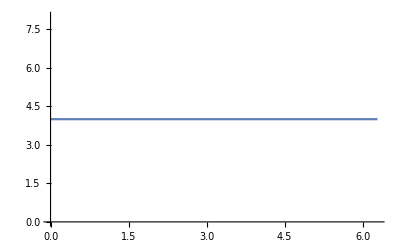

```mathematica
Plot[MatrixRank[R3[θ]],{θ,0,2π}]
```

```mathematica
gen3 = D[R3[θ],θ]/.θ->0;gen3//MatrixForm
```

(0 | -3 | 0 | 0
1 | 0 | -2 | 0
0 | 2 | 0 | -1
0 | 0 | 3 | 0)

```mathematica
Together@MatrixExp[gen3 θ]//MatrixForm//FullSimplify//TrigReduce
```

(Cos[θ]^3 | -3 Cos[θ]^2 Sin[θ] | 3 Cos[θ] Sin[θ]^2 | -Sin[θ]^3
Cos[θ]^2 Sin[θ] | 1/4 (Cos[θ]+3 Cos[3 θ]) | 1/4 (Sin[θ]-3 Sin[3 θ]) | Cos[θ] Sin[θ]^2
Cos[θ] Sin[θ]^2 | 1/4 (-Sin[θ]+3 Sin[3 θ]) | 1/4 (Cos[θ]+3 Cos[3 θ]) | -Cos[θ]^2 Sin[θ]
Sin[θ]^3 | 3 Cos[θ] Sin[θ]^2 | 3 Cos[θ]^2 Sin[θ] | Cos[θ]^3)

```mathematica
NullSpace[gen3]
```

{}

```mathematica
Subscript[PU, inv]=Inverse[Subscript[PU, 1]];Subscript[PU, inv]//MatrixForm
```

((u_(2,2))/(-u_(1,2) u_(2,1)+u_(1,1) u_(2,2)) | -(u_(1,2))/(-u_(1,2) u_(2,1)+u_(1,1) u_(2,2))
-(u_(2,1))/(-u_(1,2) u_(2,1)+u_(1,1) u_(2,2)) | (u_(1,1))/(-u_(1,2) u_(2,1)+u_(1,1) u_(2,2)))

```mathematica
Subscript[s, 1,1]=Subscript[PU, inv][[1,1]];
```

```mathematica
Subscript[s, 1,2]=Subscript[PU, inv][[1,2]];
```

```mathematica
Subscript[s, 2,1]=Subscript[PU, inv][[2,1]];
```

```mathematica
Subscript[s, 2,2]=Subscript[PU, inv][[2,2]];
```

```mathematica
Subscript[P2U, inv]=Subscript[PU, 2]/.Flatten@Table[Subscript[u, i,j]->Subscript[PU, inv][[i,j]],{i,1,2},{j,1,2}];Subscript[P2U, inv]//FullSimplify//MatrixForm
```

((u_(2,2)^2)/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2 | -(2 u_(1,2) u_(2,2))/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2 | (u_(1,2)^2)/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2
-(u_(2,1) u_(2,2))/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2 | (u_(1,2) u_(2,1)+u_(1,1) u_(2,2))/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2 | -(u_(1,1) u_(1,2))/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2
(u_(2,1)^2)/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2 | -(2 u_(1,1) u_(2,1))/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2 | (u_(1,1)^2)/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2)

```mathematica
Subscript[PU2, inv]=Inverse[Subscript[PU, 2]];Subscript[PU2, inv]//FullSimplify//MatrixForm
```

((u_(2,2)^2)/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2 | -(2 u_(1,2) u_(2,2))/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2 | (u_(1,2)^2)/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2
-(u_(2,1) u_(2,2))/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2 | (u_(1,2) u_(2,1)+u_(1,1) u_(2,2))/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2 | -(u_(1,1) u_(1,2))/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2
(u_(2,1)^2)/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2 | -(2 u_(1,1) u_(2,1))/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2 | (u_(1,1)^2)/(u_(1,2) u_(2,1)-u_(1,1) u_(2,2))^2)

```mathematica
Subscript[P2U, inv]-Subscript[PU2, inv]//FullSimplify//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)